```mathematica
α=1;β=1;γ=1;δ=1;
```

```mathematica
p1eq=D[u[t],{t,2}]==6 u[t]^2+t
```

u''[t]==t+6 u[t]^2

```mathematica
p1sln=u[t]/.First@NDSolve[{p1eq,u[0]==0,u'[0]==0},u[t],{t,0,1}]
```

InterpolatingFunction[…][t]

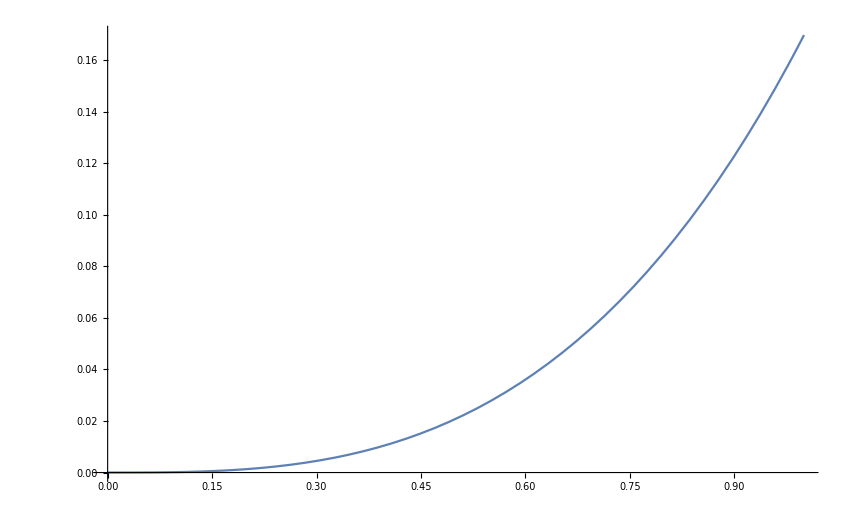

```mathematica
Plot[p1sln,{t,0,1}]
```

```mathematica
For[gridres=100,gridres<501,gridres+=100,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[p1sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_I_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
p2eq=D[u[t],{t,2}]==2 u[t]^3+t u[t]+α
```

u''[t]==1+t u[t]+2 u[t]^3

```mathematica
p2sln=u[t]/.First@NDSolve[{p2eq,u[0]==0,u'[0]==0},u[t],{t,0,1}]
```

InterpolatingFunction[…][t]

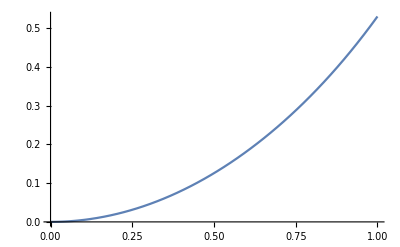

```mathematica
Plot[p2sln,{t,0,1}]
```

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[p2sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_II_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
For[gridres=100,gridres<501,gridres+=100,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[p2sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_II_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
p3eq=t u[t]*D[u[t],{t,2}]==t D[u[t],t]^2-u[t] D[u[t],t]+δ t+β u[t]+α u[t]^3+γ t u[t]^4
```

t u[t] u''[t]==t+u[t]+u[t]^3+t u[t]^4-u[t] u'[t]+t u'[t]^2

```mathematica
p3sln=u[t]/.First@NDSolve[{p3eq,u[1]==1,u'[1]==0},u[t],{t,1/4,2.1}]
```

InterpolatingFunction[…][t]

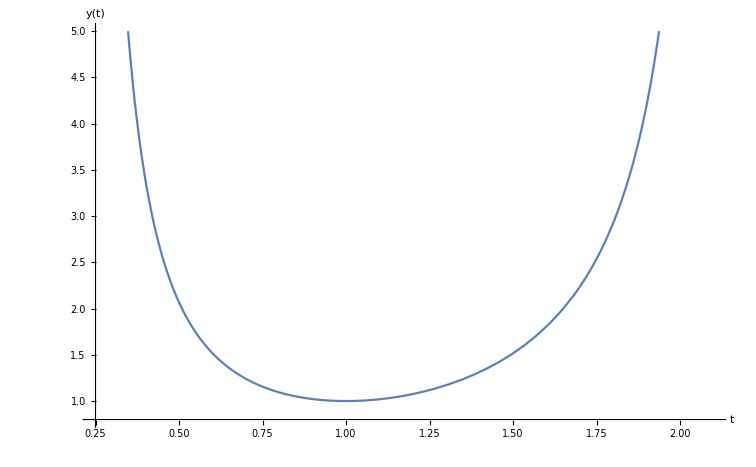

```mathematica
Plot[p3sln,{t,1/4,2.1},PlotRange->{0.8,5},AxesLabel->{"t","y(t)"},BaseStyle->{FontSize->24,Bold}]
```

```mathematica
chebgrid[a_,b_,n_]:=Table[(a+b)/2+(b-a)/2 Cos[(k π)/n],{k,n,0,-1}];
```

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=Table[t,{t,1/4,2.1,(2.1-1/4)/gridres}];
tab=Table[p3sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_III_uniform_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
For[gridres=100,gridres<501,gridres+=100,
grid=Table[t,{t,1/4,2.1,(2.1-1/4)/gridres}];
tab=Table[p3sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_III_uniform_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=chebgrid[1/4,2.1,gridres];
tab=Table[p3sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_III_chebgrid_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
For[gridres=100,gridres<501,gridres+=100,
grid=chebgrid[1/4,2.1,gridres];
tab=Table[p3sln,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_III_chebgrid_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
p4eq= u[t]*D[u[t],{t,2}]==1/2*D[u[t],t]^2+β+2*(t^2-α)u[t]^2+4t u[t]^3+3/2* u[t]^4
```

u[t] u''[t]==1+2 (-1+t^2) u[t]^2+4 t u[t]^3+(3 u[t]^4)/2+1/2 u'[t]^2

```mathematica
p4sln=u[t]/.First@NDSolve[{p4eq,u[1]==1,u'[1]==0},u[t],{t,1/4,7/4}]
```

InterpolatingFunction[…][t]

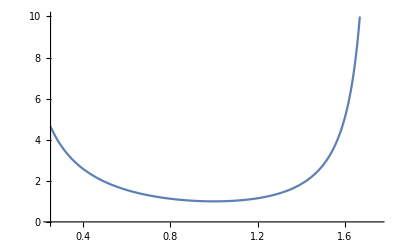

```mathematica
Plot[p4sln,{t,1/4,7/4},PlotRange->{0,10}]
```

```mathematica
p4sln/.t->1/4
```

4.63678

```mathematica
p4sln/.t->7/4
```

167.894

```mathematica
grid=Table[t,{t,1/4,7/4,(7/4-1/4)/301}]
```

{1/4,307/1204,313/1204,319/1204,325/1204,331/1204,337/1204,49/172,349/1204,355/1204,361/1204,367/1204,373/1204,379/1204,55/172,391/1204,397/1204,403/1204,409/1204,415/1204,421/1204,61/172,433/1204,439/1204,445/1204,451/1204,457/1204,463/1204,67/172,475/1204,481/1204,487/1204,493/1204,499/1204,505/1204,73/172,517/1204,523/1204,529/1204,535/1204,541/1204,547/1204,79/172,13/28,565/1204,571/1204,577/1204,583/1204,589/1204,85/172,601/1204,607/1204,613/1204,619/1204,625/1204,631/1204,91/172,643/1204,649/1204,655/1204,661/1204,667/1204,673/1204,97/172,685/1204,691/1204,697/1204,703/1204,709/1204,715/1204,103/172,727/1204,733/1204,739/1204,745/1204,751/1204,757/1204,109/172,769/1204,775/1204,781/1204,787/1204,793/1204,799/1204,115/172,811/1204,19/28,823/1204,829/1204,835/1204,841/1204,121/172,853/1204,859/1204,865/1204,871/1204,877/1204,883/1204,127/172,895/1204,901/1204,907/1204,913/1204,919/1204,925/1204,133/172,937/1204,943/1204,949/1204,955/1204,961/1204,967/1204,139/172,979/1204,985/1204,991/1204,997/1204,1003/1204,1009/1204,145/172,1021/1204,1027/1204,1033/1204,1039/1204,1045/1204,1051/1204,151/172,1063/1204,1069/1204,25/28,1081/1204,1087/1204,1093/1204,157/172,1105/1204,1111/1204,1117/1204,1123/1204,1129/1204,1135/1204,163/172,1147/1204,1153/1204,1159/1204,1165/1204,1171/1204,1177/1204,169/172,1189/1204,1195/1204,1201/1204,1207/1204,1213/1204,1219/1204,175/172,1231/1204,1237/1204,1243/1204,1249/1204,1255/1204,1261/1204,181/172,1273/1204,1279/1204,1285/1204,1291/1204,1297/1204,1303/1204,187/172,1315/1204,1321/1204,1327/1204,31/28,1339/1204,1345/1204,193/172,1357/1204,1363/1204,1369/1204,1375/1204,1381/1204,1387/1204,199/172,1399/1204,1405/1204,1411/1204,1417/1204,1423/1204,1429/1204,205/172,1441/1204,1447/1204,1453/1204,1459/1204,1465/1204,1471/1204,211/172,1483/1204,1489/1204,1495/1204,1501/1204,1507/1204,1513/1204,217/172,1525/1204,1531/1204,1537/1204,1543/1204,1549/1204,1555/1204,223/172,1567/1204,1573/1204,1579/1204,1585/1204,37/28,1597/1204,229/172,1609/1204,1615/1204,1621/1204,1627/1204,1633/1204,1639/1204,235/172,1651/1204,1657/1204,1663/1204,1669/1204,1675/1204,1681/1204,241/172,1693/1204,1699/1204,1705/1204,1711/1204,1717/1204,1723/1204,247/172,1735/1204,1741/1204,1747/1204,1753/1204,1759/1204,1765/1204,253/172,1777/1204,1783/1204,1789/1204,1795/1204,1801/1204,1807/1204,259/172,1819/1204,1825/1204,1831/1204,1837/1204,1843/1204,43/28,265/172,1861/1204,1867/1204,1873/1204,1879/1204,1885/1204,1891/1204,271/172,1903/1204,1909/1204,1915/1204,1921/1204,1927/1204,1933/1204,277/172,1945/1204,1951/1204,1957/1204,1963/1204,1969/1204,1975/1204,283/172,1987/1204,1993/1204,1999/1204,2005/1204,2011/1204,2017/1204,289/172,2029/1204,2035/1204,2041/1204,2047/1204,2053/1204,2059/1204,295/172,2071/1204,2077/1204,2083/1204,2089/1204,2095/1204,2101/1204,7/4}

```mathematica
tab=Table[p4sln/.t->t1,{t1,grid}]
```

{4.63678,4.52246,4.41329,4.30892,4.20904,4.11335,4.02161,3.93357,3.849,3.76772,3.68952,3.61423,3.5417,3.47178,3.40432,3.3392,3.2763,3.21551,3.15673,3.09985,3.04479,2.99146,2.93978,2.88967,2.84108,2.79393,2.74815,2.7037,2.66051,2.61853,2.57772,2.53803,2.49941,2.46182,2.42523,2.3896,2.35488,2.32106,2.28808,2.25594,2.22459,2.19401,2.16418,2.13506,2.10664,2.07889,2.05179,2.02532,1.99947,1.9742,1.94951,1.92538,1.90179,1.87872,1.85617,1.83411,1.81253,1.79142,1.77077,1.75056,1.73078,1.71143,1.69249,1.67395,1.65579,1.63802,1.62062,1.60358,1.5869,1.57057,1.55457,1.5389,1.52356,1.50853,1.49381,1.4794,1.46528,1.45145,1.43791,1.42465,1.41166,1.39894,1.38649,1.37429,1.36235,1.35065,1.3392,1.328,1.31703,1.30629,1.29578,1.2855,1.27544,1.26559,1.25597,1.24655,1.23734,1.22834,1.21955,1.21095,1.20255,1.19435,1.18634,1.17852,1.17089,1.16344,1.15618,1.1491,1.1422,1.13548,1.12894,1.12256,1.11637,1.11034,1.10449,1.0988,1.09328,1.08793,1.08274,1.07772,1.07286,1.06816,1.06362,1.05924,1.05502,1.05096,1.04706,1.04331,1.03972,1.03629,1.03301,1.02989,1.02692,1.02411,1.02145,1.01895,1.0166,1.0144,1.01236,1.01048,1.00874,1.00717,1.00575,1.00448,1.00337,1.00242,1.00162,1.00098,1.0005,1.00018,1.00002,1.00002,1.00018,1.00051,1.001,1.00165,1.00247,1.00346,1.00462,1.00595,1.00745,1.00913,1.01098,1.01301,1.01523,1.01762,1.0202,1.02296,1.02592,1.02906,1.03241,1.03594,1.03968,1.04363,1.04778,1.05213,1.05671,1.0615,1.06651,1.07174,1.07721,1.0829,1.08884,1.09501,1.10144,1.10812,1.11505,1.12225,1.12971,1.13745,1.14547,1.15378,1.16239,1.17129,1.1805,1.19003,1.19988,1.21007,1.22059,1.23147,1.24271,1.25431,1.2663,1.27867,1.29145,1.30464,1.31826,1.33231,1.34682,1.36179,1.37724,1.39319,1.40965,1.42664,1.44418,1.46228,1.48096,1.50025,1.52016,1.54072,1.56196,1.58389,1.60654,1.62994,1.65412,1.67911,1.70494,1.73164,1.75926,1.78782,1.81737,1.84796,1.87961,1.91239,1.94633,1.98151,2.01796,2.05575,2.09495,2.13562,2.17783,2.22167,2.26721,2.31453,2.36374,2.41494,2.46822,2.52372,2.58155,2.64184,2.70474,2.7704,2.83899,2.9107,2.98572,3.06426,3.14655,3.23285,3.32343,3.41859,3.51867,3.62402,3.73504,3.85217,3.9759,4.10676,4.24535,4.39233,4.54845,4.71453,4.89152,5.08047,5.28257,5.49919,5.73188,5.98242,6.25286,6.5456,6.86339,7.20951,7.58779,8.00279,8.46,8.96603,9.52894,10.1587,10.8677,11.6717,12.5906,13.6509,14.8871,16.3467,18.0955,20.2279,22.8846,26.2847,30.789,37.0367,46.2782,61.3354,90.201,167.894}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export[StringJoin["wolfram_sln/","p_IV_sln_",ToString[301],".csv"],tab]
```

wolfram_sln/p_IV_sln_301.csv

```mathematica
p5eqinit=u''[t]==(1/(2u[t])+1/(u[t]-1))(u'[t])^2-1/t  u'[t]+(u[t]-1)^2/t^2(α u[t]+β/u[t])+γ u[t]/t+δ (u[t](u[t]+1))/(u[t]-1)
```

u''[t]==(γ u[t])/t+(δ u[t] (1+u[t]))/(-1+u[t])+((-1+u[t])^2 (β/u[t]+α u[t]))/t^2-u'[t]/t+(1/(-1+u[t])+1/(2 u[t])) u'[t]^2

```mathematica
((1/(2u[t])+1/(u[t]-1))(u'[t])^2-1/t  u'[t]+(u[t]-1)^2/t^2(α u[t]+β/u[t])+γ u[t]/t+δ (u[t](u[t]+1))/(u[t]-1))*(2 t^2 u[t]*(u[t]-1))//Expand//Simplify
```

-2 β+2 (3 α+β+t (γ+t δ)) u[t]^3-6 α u[t]^4+2 α u[t]^5-t^2 u'[t]^2-2 u[t]^2 (α+3 β+t γ-t^2 δ+t u'[t])+u[t] (6 β+2 t u'[t]+3 t^2 u'[t]^2)

```mathematica
rhs=-2 β+2 (3 α+β+t (γ+t δ)) u[t]^3-6 α u[t]^4+2 α u[t]^5-t^2 u'[t]^2-2 u[t]^2 (α+3 β+t γ-t^2 δ+t u'[t])+u[t] (6 β+2 t u'[t]+3 t^2 u'[t]^2)
```

-2 β+2 (3 α+β+t (γ+t δ)) u[t]^3-6 α u[t]^4+2 α u[t]^5-t^2 u'[t]^2-2 u[t]^2 (α+3 β+t γ-t^2 δ+t u'[t])+u[t] (6 β+2 t u'[t]+3 t^2 u'[t]^2)

```mathematica
p5eq=(2 t^2 u[t]*(u[t]-1))*u''[t]-rhs==0
```

2-2 (4+t+t^2) u[t]^3+6 u[t]^4-2 u[t]^5+t^2 u'[t]^2-2 u[t]^2 (-4-t+t^2-t u'[t])-u[t] (6+2 t u'[t]+3 t^2 u'[t]^2)+2 t^2 (-1+u[t]) u[t] u''[t]==0

```mathematica
(2 t^2 u[t]*(u[t]-1))*u''[t]//Expand
```

-2 t^2 u[t] u''[t]+2 t^2 u[t]^2 u''[t]

```mathematica
-rhs//Expand
```

2 β-6 β u[t]+2 α u[t]^2+6 β u[t]^2+2 t γ u[t]^2-2 t^2 δ u[t]^2-6 α u[t]^3-2 β u[t]^3-2 t γ u[t]^3-2 t^2 δ u[t]^3+6 α u[t]^4-2 α u[t]^5-2 t u[t] u'[t]+2 t u[t]^2 u'[t]+t^2 u'[t]^2-3 t^2 u[t] u'[t]^2

```mathematica
-rhs==2 β-6 β u[t]+2 (α+3 β+t (γ-t δ)) u[t]^2-2 (3 α+β+t (γ+t δ)) u[t]^3+6 α u[t]^4-2 α u[t]^5-2 t u[t] u'[t]+2 t u[t]^2 u'[t]+t^2 u'[t]^2-3 t^2 u[t] u'[t]^2//FullSimplify
```

True

```mathematica
rhs2=-(2 β-6 β u[t]+2 (α+3 β+t (γ-t δ)) u[t]^2-2 (3 α+β+t (γ+t δ)) u[t]^3+6 α u[t]^4-2 α u[t]^5-2 t u[t] u'[t]+2 t u[t]^2 u'[t]+t^2 u'[t]^2-3 t^2 u[t] u'[t]^2)
```

-2 β+6 β u[t]-2 (α+3 β+t (γ-t δ)) u[t]^2+2 (3 α+β+t (γ+t δ)) u[t]^3-6 α u[t]^4+2 α u[t]^5+2 t u[t] u'[t]-2 t u[t]^2 u'[t]-t^2 u'[t]^2+3 t^2 u[t] u'[t]^2

```mathematica
p5eq=(2 t^2 u[t]*(u[t]-1))*u''[t]-rhs==0
```

2 β-2 (3 α+β+t (γ+t δ)) u[t]^3+6 α u[t]^4-2 α u[t]^5+t^2 u'[t]^2+2 u[t]^2 (α+3 β+t γ-t^2 δ+t u'[t])-u[t] (6 β+2 t u'[t]+3 t^2 u'[t]^2)+2 t^2 (-1+u[t]) u[t] u''[t]==0

```mathematica
2 α u[t]^2+6 β u[t]^2+2 t γ u[t]^2-2 t^2 δ u[t]^2//FullSimplify
```

2 (α+3 β+t (γ-t δ)) u[t]^2

```mathematica
-6 α u[t]^3-2 β u[t]^3-2 t γ u[t]^3-2 t^2 δ u[t]^3//FullSimplify
```

-2 (3 α+β+t (γ+t δ)) u[t]^3

```mathematica
p5eq/.t->1
```

2 (-1+u[1]) u[1] u''[1]==-2+12 u[1]^3-6 u[1]^4+2 u[1]^5+2 u[1]^2 (-4-u'[1])-u'[1]^2+u[1] (6+2 u'[1]+3 u'[1]^2)

```mathematica
p5slninit=u[t]/.First@NDSolve[{p5eq,u[0.9]==2.979325765542575,u[1.2]==4.117945909429169},u[t],{t,0.9,1.2}]
```

InterpolatingFunction[…][t]

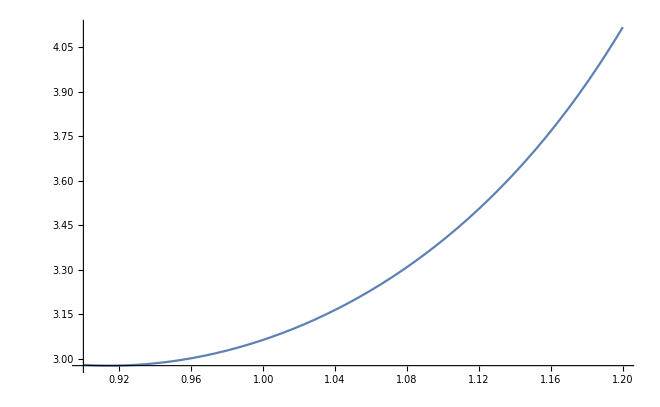

```mathematica
Plot[p5slninit,{t,0.9,1.2}]
```

```mathematica
p6eqinit=u''[t]==1/2(1/u[t]+1/(u[t]-1)+1/(u[t]-t))(u'[t])^2-(1/t+1/(t-1)+1/(u[t]-t))  u'[t]+(u[t](u[t]-1)(u[t]-t))/(t^2(t-1)^2)(α+β t/u[t]^2+γ(t-1)/(u[t]-1)^2+δ(t(t-1))/(u[t]-t)^2)
```

u''[t]==((-1+u[t]) u[t] (-t+u[t]) (α+((-1+t) γ)/(-1+u[t])^2+(t β)/u[t]^2+((-1+t) t δ)/(-t+u[t])^2))/((-1+t)^2 t^2)-(1/(-1+t)+1/t+1/(-t+u[t])) u'[t]+1/2 (1/(-1+u[t])+1/u[t]+1/(-t+u[t])) u'[t]^2

```mathematica
(1/2(1/u[t]+1/(u[t]-1)+1/(u[t]-t))(u'[t])^2-(1/t+1/(t-1)+1/(u[t]-t))  u'[t]+(u[t](u[t]-1)(u[t]-t))/(t^2(t-1)^2)(α+β t/u[t]^2+γ(t-1)/(u[t]-1)^2+δ(t(t-1))/(u[t]-t)^2))*(-1+t)^2 t^2(u[t]-t)(u[t]-1)u[t]//ExpandAll//FullSimplify
```

(α+t (4+t) α-γ+t (β+γ+(-1+t) δ)) u[t]^4-2 (1+t) α u[t]^5+α u[t]^6-t u[t]^3 (2 ((1+t) α+(1+t) β+(-1+t) (γ+δ))+(-1+t) (-1+2 t) u'[t])+1/2 t^3 (2 β+(-1+t)^2 u'[t]^2)+1/2 t u[t]^2 (2 (β-δ+t (α+(4+t) β+(-1+t) γ+δ))+u'[t] (2+2 t (-3+t+t^2)+3 (-1+t)^2 t u'[t]))-t^2 u[t] (2 (1+t) β+(-1+t) u'[t] (t+(-1+t^2) u'[t]))

```mathematica
rhs6eq=(α+t (4+t) α-γ+t (β+γ+(-1+t) δ)) u[t]^4-2 (1+t) α u[t]^5+α u[t]^6-t u[t]^3 (2 ((1+t) α+(1+t) β+(-1+t) (γ+δ))+(-1+t) (-1+2 t) u'[t])+1/2 t^3 (2 β+(-1+t)^2 u'[t]^2)+1/2 t u[t]^2 (2 (β-δ+t (α+(4+t) β+(-1+t) γ+δ))+u'[t] (2+2 t (-3+t+t^2)+3 (-1+t)^2 t u'[t]))-t^2 u[t] (2 (1+t) β+(-1+t) u'[t] (t+(-1+t^2) u'[t]))
```

(α+t (4+t) α-γ+t (β+γ+(-1+t) δ)) u[t]^4-2 (1+t) α u[t]^5+α u[t]^6-t u[t]^3 (2 ((1+t) α+(1+t) β+(-1+t) (γ+δ))+(-1+t) (-1+2 t) u'[t])+1/2 t^3 (2 β+(-1+t)^2 u'[t]^2)+1/2 t u[t]^2 (2 (β-δ+t (α+(4+t) β+(-1+t) γ+δ))+u'[t] (2+2 t (-3+t+t^2)+3 (-1+t)^2 t u'[t]))-t^2 u[t] (2 (1+t) β+(-1+t) u'[t] (t+(-1+t^2) u'[t]))

```mathematica
(-1+t)^2 t^2(u[t]-t)(u[t]-1)u[t]*u''[t]==2 (α+t (4+t) α-γ+t (β+γ+(-1+t) δ)) u[t]^4-4 (1+t) α u[t]^5+2 α u[t]^6-2 t u[t]^3 (2 ((1+t) α+(1+t) β+(-1+t) (γ+δ))+(-1+t) (-1+2 t) u'[t])+t^3 (2 β+(-1+t)^2 u'[t]^2)+t u[t]^2 (2 (β-δ+t (α+(4+t) β+(-1+t) γ+δ))+u'[t] (2+2 t (-3+t+t^2)+3 (-1+t)^2 t u'[t]))-2 t^2 u[t] (2 (1+t) β+(-1+t) u'[t] (t+(-1+t^2) u'[t]))
```

(-1+t)^2 t^2 (-1+u[t]) u[t] (-t+u[t]) u''[t]==2 (α+t (4+t) α-γ+t (β+γ+(-1+t) δ)) u[t]^4-4 (1+t) α u[t]^5+2 α u[t]^6-2 t u[t]^3 (2 ((1+t) α+(1+t) β+(-1+t) (γ+δ))+(-1+t) (-1+2 t) u'[t])+t^3 (2 β+(-1+t)^2 u'[t]^2)+t u[t]^2 (2 (β-δ+t (α+(4+t) β+(-1+t) γ+δ))+u'[t] (2+2 t (-3+t+t^2)+3 (-1+t)^2 t u'[t]))-2 t^2 u[t] (2 (1+t) β+(-1+t) u'[t] (t+(-1+t^2) u'[t]))

```mathematica
c60=-t^3 β;
c61=2 t^2 (1+t) β ;
c62=-t (β-δ+t (α+(4+t) β+(-1+t) γ+δ)) ;
c63=2 t ((1+t) α+(1+t) β+(-1+t) (γ+δ));
c64=-(α+t (4+t) α-γ+t (β+γ+(-1+t) δ));
c65=2 (1+t) α;
c66=(-1+t) t^3 ;
c67=-t (1+t (-3+t+t^2));
c68=(-1+t) t (-1+2 t);
c69=-1/2 (-1+t)^2 t^3;
c610=(-1+t)^2 t^2 (1+t);
c611=-3/2 (-1+t)^2 t^2;
c612=(-1+t)^2 t^3;
c613=-(-1+t)^2 t^2 (1+t);
c614=(-1+t)^2 t^2;
```

```mathematica
(-1+t)^2 t^2(u[t]-t)(u[t]-1)u[t]*u''[t]-rhs6eq==c60+c61 u[t]+c62 u[t]^2+c63 u[t]^3+c64 u[t]^4+c65 u[t]^5-α u[t]^6+c66 u[t] u'[t]+c67 u[t]^2 u'[t]+c68 u[t]^3 u'[t]+c69 u'[t]^2+c610 u[t] u'[t]^2+c611 u[t]^2 u'[t]^2+c612 u[t] u''[t]+c613 u[t]^2 u''[t]+c614 u[t]^3 u''[t]//FullSimplify
```

True

```mathematica
p6eq=c60+c61 u[t]+c62 u[t]^2+c63 u[t]^3+c64 u[t]^4+c65 u[t]^5-α u[t]^6+c66 u[t] u'[t]+c67 u[t]^2 u'[t]+c68 u[t]^3 u'[t]+c69 u'[t]^2+c610 u[t] u'[t]^2+c611 u[t]^2 u'[t]^2+c612 u[t] u''[t]+c613 u[t]^2 u''[t]+c614 u[t]^3 u''[t]==0
```

-t^3 β+2 t^2 (1+t) β u[t]-t (β-δ+t (α+(4+t) β+(-1+t) γ+δ)) u[t]^2+2 t ((1+t) α+(1+t) β+(-1+t) (γ+δ)) u[t]^3+(-α-t (4+t) α+γ-t (β+γ+(-1+t) δ)) u[t]^4+2 (1+t) α u[t]^5-α u[t]^6+(-1+t) t^3 u[t] u'[t]-t (1+t (-3+t+t^2)) u[t]^2 u'[t]+(-1+t) t (-1+2 t) u[t]^3 u'[t]-1/2 (-1+t)^2 t^3 u'[t]^2+(-1+t)^2 t^2 (1+t) u[t] u'[t]^2-3/2 (-1+t)^2 t^2 u[t]^2 u'[t]^2+(-1+t)^2 t^3 u[t] u''[t]-(-1+t)^2 t^2 (1+t) u[t]^2 u''[t]+(-1+t)^2 t^2 u[t]^3 u''[t]==0

```mathematica
p6eq
```

-t^3 β+2 t^2 (1+t) β u[t]-t (β-δ+t (α+(4+t) β+(-1+t) γ+δ)) u[t]^2+2 t ((1+t) α+(1+t) β+(-1+t) (γ+δ)) u[t]^3+(-α-t (4+t) α+γ-t (β+γ+(-1+t) δ)) u[t]^4+2 (1+t) α u[t]^5-α u[t]^6+(-1+t) t^3 u[t] u'[t]-t (1+t (-3+t+t^2)) u[t]^2 u'[t]+(-1+t) t (-1+2 t) u[t]^3 u'[t]-1/2 (-1+t)^2 t^3 u'[t]^2+(-1+t)^2 t^2 (1+t) u[t] u'[t]^2-3/2 (-1+t)^2 t^2 u[t]^2 u'[t]^2+(-1+t)^2 t^3 u[t] u''[t]-(-1+t)^2 t^2 (1+t) u[t]^2 u''[t]+(-1+t)^2 t^2 u[t]^3 u''[t]==0

```mathematica
p6eq/.t->1
```

-β+4 β u[1]-(α+6 β) u[1]^2+2 (2 α+2 β) u[1]^3+(-6 α-β) u[1]^4+4 α u[1]^5-α u[1]^6==0

```mathematica
p6eq/.t->2
```

-8+24 u[2]-36 u[2]^2+32 u[2]^3-18 u[2]^4+6 u[2]^5-u[2]^6+8 u[2] u'[2]-14 u[2]^2 u'[2]+6 u[2]^3 u'[2]-4 u'[2]^2+12 u[2] u'[2]^2-6 u[2]^2 u'[2]^2+8 u[2] u''[2]-12 u[2]^2 u''[2]+4 u[2]^3 u''[2]==0

```mathematica
p6slninit=u[t]/.First@NDSolve[{p6eq,u[1.2]==2,u[1.4]==2},u[t],{t,1.2,1.4}]
```

InterpolatingFunction[…][t]

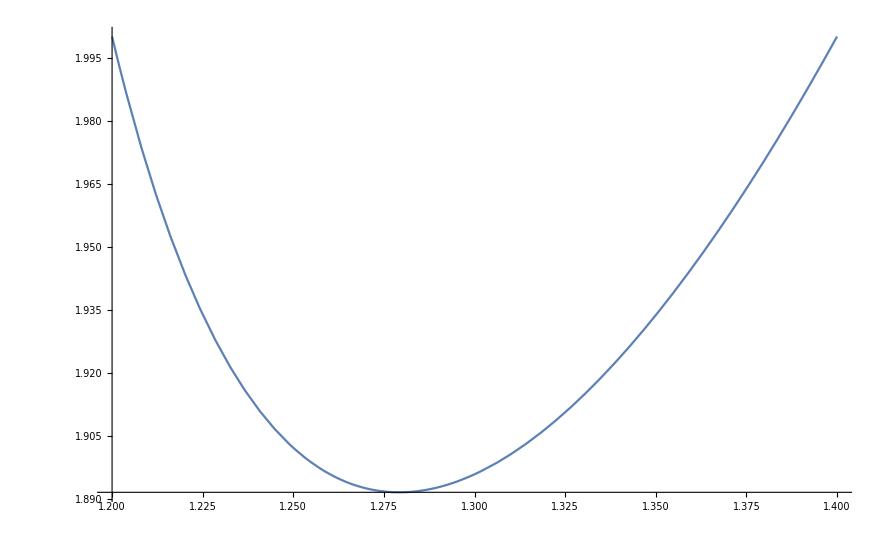

```mathematica
Plot[p6slninit,{t,1.2,1.4}]
```

```mathematica
For[gridres=100,gridres<501,gridres+=100,
grid=Table[t,{t,1.2,1.4,(1.4-1.2)/gridres}];
tab=Table[p6slninit,{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","P_VI_sln_",ToString[gridres],".csv"],tab]
]
```